## 3 Plasma Approach

## 3.1 Prep

```mathematica
(*variables*)
mt=mi+mj;T0=0.5*(mi*ui^2+mj*uj^2);V=(mi*ui+mj*uj)/mt;T0d=T0-0.5*mt*V^2;μ=mi*mj/mt//Simplify;tmax=0.01;
```

```mathematica
(*mathieu trajectories*)
D2n[n_]:=(a-(2*n+β)^2)/q;
recur[i_,stop_,dir_]:=1/(D2n[i*dir]-If[i≥stop,0,recur[i+1,stop,dir]])//FullSimplify;

getBetaEQ[ordD_,ordAQ_]:=Normal[Series[a-q*(recur[1,ordD+1,1]+recur[1,ordD+1,-1])/.{a->ϵ*a,q->ϵ*q,β->ϵ*β},{ϵ,0,ordAQ+1}]]/.{ϵ->1};
solveMathieu[ordD_,ordAQ_]:=Solve[β^2==getBetaEQ[ordD,ordAQ],β,PositiveReals]//FullSimplify (*This is just for ease of use*)

rMat[A0_,B0_,ad_,qd_,ord_]:=Module[{C2n=recur[#,ord,1]&/@Range[ord],Cn2n=recur[#,ord,-1]&/@Range[ord]},
C2n=Apply[Times,C2n[[;;#]]]&/@Range[ord];Cn2n=Apply[Times,Cn2n[[;;#]]]&/@Range[ord];
(A0*Cos[β*t]+B0*Sin[β*t])+Sum[C2n[[n]]*(A0*Cos[(2*n+β)*t]+B0*Sin[(2*n+β)*t])+Cn2n[[n]]*(A0*Cos[(-2*n+β)*t]+B0*Sin[(-2*n+β)*t]),{n,1,ord}]/.Normal[solveMathieu[ord,ord]]/.{a->ad,q->qd}//FullSimplify]
```

```mathematica
(*magic*)
Δp=-4*μ*b^2*(ri-rj)*Sqrt[2*μ*T0d]*(ui-uj)/(b^2+(rj-ri)^2)^2//FullSimplify;
dpdt=dplldt*ui//FullSimplify;
b0=Table[Abs[z0M[[1]]-z0M[[i]]]*l0/.solnsMOTION,{i,2,Num}];db=5*^-6;
```

## 3.2 Setup

```mathematica
ahold=0.01;qhold=0.1;ordhold=3;βhold=Normal[solveMathieu[4,4]][[1]];mi=171*1.66*^-27;mj=138*1.66*^-27;
iIC={0,31.189};jIC={0,3.471};
```

```mathematica
ri[td_]:=Evaluate[rMat[Ai,Bi,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];rj[td_]:=Evaluate[rMat[Aj,Bj,ahold,qhold,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];
ui[td_]:=D[ri[t],t]/.{t->td};uj[td_]:=D[rj[t],t]/.{t->td};
```

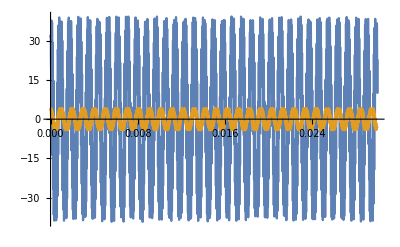

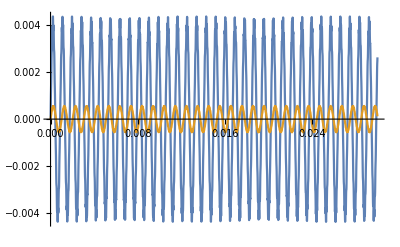

```mathematica
iVals=Solve[{ri[0]==iIC[[1]],ui[0]==iIC[[2]]},{Ai,Bi}][[1]];
jVals=Solve[{rj[0]==jIC[[1]],uj[0]==jIC[[2]]},{Aj,Bj}][[1]];
rif[t_]:=ri[t]/.iVals//FullSimplify;rjf[t_]:=rj[t]/.jVals//FullSimplify;
uif[t_]:=ui[t]/.iVals//FullSimplify;ujf[t_]:=uj[t]/.jVals//FullSimplify;

Plot[{Evaluate[Re[uif[t]]],Evaluate[Re[ujf[t-0.003]]]},{t,0,0.03}]
Plot[{Evaluate[Re[rif[t]]],Evaluate[Re[rjf[t]]]},{t,0,0.03}]
```

## 3.3 Average over Mathieu trajectories

```mathematica
ri1[td_]:=Evaluate[rMat[Ai1,Bi1,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];
ri2[td_]:=Evaluate[rMat[Ai2,Bi2,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];
ui1[td_]:=D[ri1[t],t]/.{t->td};ui2[td_]:=D[ri2[t],t]/.{t->td};
iVals2=Solve[{ri1[0]==iIC[[1]],ui1[0]==iIC[[2]]},{Ai1,Bi1}][[1]];Ai1=Ai1/.iVals2;Bi1=Bi1/.iVals2;
```

```mathematica
fn[td_]:=Sum[(Cos[(2*n+β)*td]-Cos[(2*n+β)*(td-2*t0)])/(2*n+β),{n,-ordhold,ordhold}]/.βhold/.{a->ahold,q->qhold}
```

```mathematica
newAidBid=Solve[{ri1[t0]==ri2[t0],ui2[t0]-ui1[t0]==dphold},{Ai2,Bi2}][[1]]/.{dphold->Δp};
Ai2=Chop[Ai2/.newAidBid]//Simplify;Bi2=Chop[Bi2/.newAidBid]//Simplify;
```

```mathematica
ri2h=Evaluate[rMat[Ai2h,Bi2h,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->t*0.5*wmhz*w/.solnsMOTION}][[1]];
ui2h=D[ri2h,t];
ri2h=Chop[ri2h/.{Ai2h->Ai2,Bi2h->Bi2}]//Simplify;
ui2h=Chop[ui2h/.{Ai2h->Ai2,Bi2h->Bi2}]//Simplify;
```

```mathematica
ΔEi=0.5*mi*(ui2h^2-ui1[t0]^2);
```

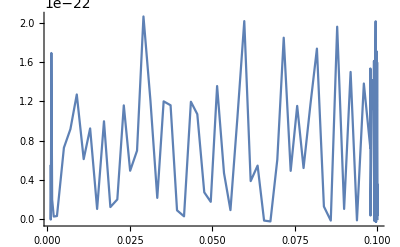

```mathematica
Plot[Evaluate[ΔEi/.{t0->0.002}],{t,0.001,0.1}]
```

## 3.4 Spitzer Approach

```mathematica
ParallelSum[NIntegrate[ΔEi,{b,b0[[i]]-db,b0[[i]]+db},{t0,0,0.01},{t,0,0.01}],{i,Num-1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

4.29616×10^-35

```mathematica
mt=mi+mj;k=8.9875*^9;e=1.602*^-19;mj=138*1.66*^-27;kb=1.38*^-23;eps=0.533;rho=(Num-1)/(Pi*b0[[-1]]*(5*^-4)^2);
b0=Table[Abs[z0M[[1]]-z0M[[i]]]*l0/.solnsMOTION,{i,2,Num}];
```

```mathematica
Ej=kb*0.1*0.5;Ei=4*e;
```

```mathematica
dEidt=Sum[-2*k*e^3*mi*mj/mt^2/Sqrt[2*mi*Ei^3]*(1-mj/mi*eps)*(Ei-Ej)*Log[1+(Ei*b0[[n]]/(k*e^2))^2],{n,Num-1}]//FullSimplify
```

(6.28437×10^-85-5.14692×10^-60 mi)/(√mi (2.2908×10^-25+mi)^2)

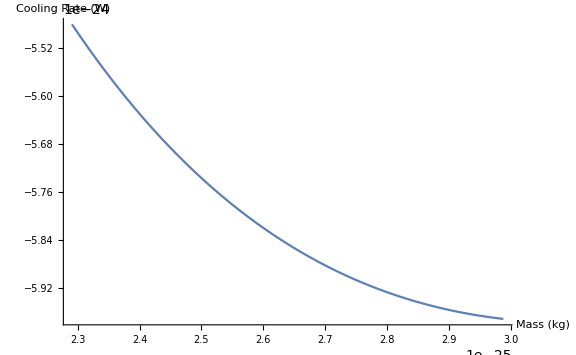

```mathematica
Plot[Evaluate[dEidt],{mi,138*1.66*^-27,180*1.66*^-27},ImageSize->Large,Axes->True,AxesLabel->{"Mass (kg)","Cooling Rate (W)"}]
```

## 3.5 Force in z-direction

```mathematica
Δpperp=-4*μ*b*(ri-rj)/(b^2+(ri-rj)^2)*(ui-uj);
Δpperp=Integrate[Δpperp,b];d2=Δpperp/.{b->b2};d1=Δpperp/.{b->b1};
Δpperp=d2-d1//FullSimplify;
```

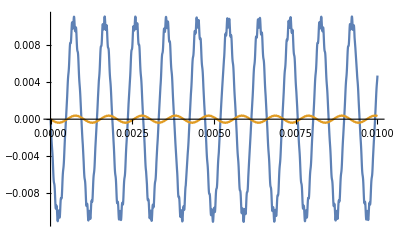

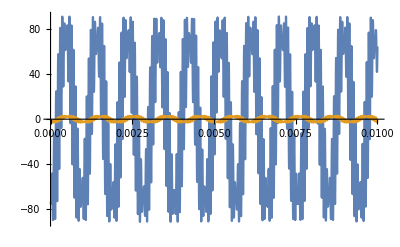

```mathematica
iVals3=Solve[{ri[0]==iIC[[1]],0.5*mi*ui[0]^2==0.5*kb*100},{Ai,Bi}][[1]];
jVals3=Solve[{rj[0]==jIC[[1]],0.5*mj*uj[0]^2==0.5*kb*0.1},{Aj,Bj}][[1]];
Δpperp=Δpperp/.{ri->ri[ti],rj->rj[tj],ui->ui[ti],uj->uj[tj]}/.iVals3/.jVals3//Simplify;

Plot[{Evaluate[ri[t]/.iVals3],Evaluate[rj[t]/.jVals3]},{t,0,tmax}]
Plot[{Evaluate[ui[t]/.iVals3],Evaluate[uj[t]/.jVals3]},{t,0,tmax}]
```

```mathematica
f[n_]:=NIntegrate[(Δpperp)^2/.{b2->b0[[1]]+db,b1->b0[[1]]-db},{ti,0,n*tmax},{tj,0,n*tmax}]/(n*tmax)^2
```

```mathematica
th=ParallelTable[f[i],{i,1,30}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.58258×10^-61 and 1.37027×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.59198×10^-60 and 4.79269×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.02171×10^-61 and 8.40783×10^-62 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.52558×10^-62 and 2.69226×10^-63 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.26637×10^-60 and 4.84755×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.75855×10^-61 and 1.1509×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.22968×10^-60 and 2.75735×10^-61 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.66862×10^-62 and 1.79666×10^-62 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.28429×10^-60 and 6.46707×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.56718×10^-61 and 1.70438×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.39045×10^-60 and 3.75191×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.92636×10^-61 and 4.12572×10^-62 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.70638×10^-60 and 7.61323×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.0307183,0.177266}. NIntegrate obtained 3.84965×10^-60 and 8.21036×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.0226811,0.211031}. NIntegrate obtained 4.04099×10^-60 and 6.96145×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.08542×10^-60 and 1.79316×10^-60 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.88641×10^-60 and 1.49084×10^-60 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.5877×10^-60 and 4.79403×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.146043,0.244796}. NIntegrate obtained 2.68143×10^-60 and 7.90982×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.63651×10^-60 and 1.06016×10^-60 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.140843,0.248957}. NIntegrate obtained 6.40109×10^-60 and 1.49717×10^-60 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.44946×10^-60 and 8.61454×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.0675829,0.253237}. NIntegrate obtained 4.82577×10^-60 and 1.31423×10^-60 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.77666×10^-60 and 1.03412×10^-60 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.05902×10^-60 and 1.26012×10^-60 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

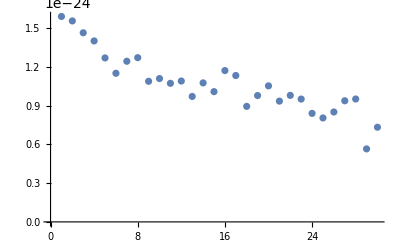

```mathematica
ListPlot[Sqrt[th]/(2*db)]
```

```mathematica
154*1.66*^-27*(0.07*wmhz)^2*Abs[z0M[[1]]*l0]-ke2*Sum[L0Mn[1,i,-2],{i,2,Num}]/l0^2/.{U->10}
```

1.28911×10^-18

```mathematica
dEidt=Sum[k*e^3/Sqrt[2*mi*Ei^3]*Log[1+(Ei*b0[[n]]/(k*e^2))^2],{n,Num-1}]//FullSimplify
```

0.0000329045

```mathematica
Max[Sqrt[th]/(2*db)]/dEidt
```

4.81451×10^-20

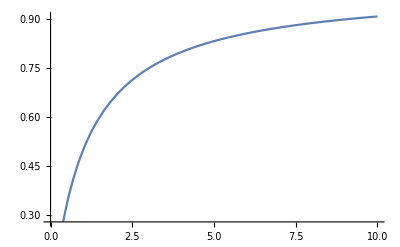

```mathematica
Plot[x/(1+x),{x,0,10}]
```